```mathematica
raw=Drop[Import[FileNameJoin[{NotebookDirectory[],"data/out.dat"}], "Table", "FieldSeparators"->{" "}, HeaderLines->1], -1];
```

```mathematica
cdata=Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]]}];
vdata=Transpose[{raw[[All, 12]], raw[[All, 13]], raw[[All, 14]]}];
pdata=raw[[All, 16]];
```

```mathematica
avgv=Mean[Sqrt[vdata[[All, 1]]^2+vdata[[All,2]]^2+vdata[[All, 3]]^2]]
```

0.0151152

```mathematica
maxv=Max[Abs[vdata]]
```

0.131906

```mathematica
l=Abs[Max[Flatten[cdata]]-Min[Flatten[cdata]]]
```

2.

```mathematica
nu=0.890*10^(-3)
```

0.00089

```mathematica
ren=avgv*l/nu
```

33.9667

```mathematica
maxren=maxv*l/nu
```

296.418

```mathematica
arrows=Table[{Arrowheads[.01],Arrow[{
cdata[[i]],cdata[[i]]+
(vdata[[i]]/(maxv))*l*0.2
}]}, {i, Length[raw]}];
```

```mathematica
gg=Graphics3D[arrows,Axes->True,AxesLabel->{"x (m)","y (m)","z (m)"},ImageSize->Large]
```

-Graphics3D-

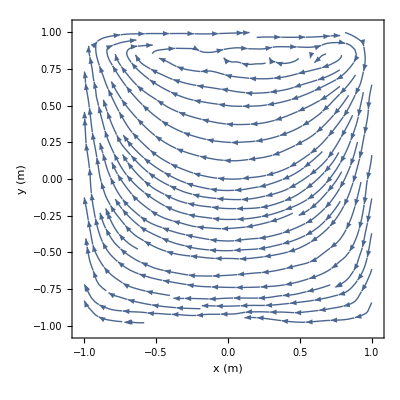

```mathematica
ListStreamPlot[Table[{{cdata[[i, 1]], cdata[[i, 2]]}, {vdata[[i, 1]], vdata[[i, 2]]}}, {i, Length[vdata]}], FrameLabel->{"x (m)","y (m)"}]
```

```mathematica
(*ListContourPlot3D[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]], raw[[All, 16]]}], PlotRange->All, PlotLegends->Automatic]*)
```

```mathematica
(*ListDensityPlot3D[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]], raw[[All, 16]]}],ColorFunction->"TemperatureMap",PlotLegends->BarLegend[All, LegendLabel->"p (Pa)"], PlotRange->All,AxesLabel->{"x (m)","y (m)","z (m)"}]*)
```

```mathematica
(*ListDensityPlot3D[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]], Sqrt[raw[[All, 12]]^2+raw[[All, 13]]^2+raw[[All, 14]]^2]}],ColorFunction->"BlueGreenYellow",PlotLegends->Automatic, PlotRange->All]*)
```

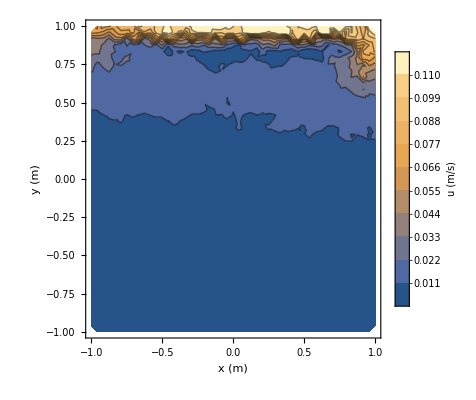

```mathematica
vmp=ListContourPlot[Transpose[{raw[[All, 8]], raw[[All, 9]], Sqrt[raw[[All, 12]]^2+raw[[All, 13]]^2+raw[[All, 14]]^2]}], PlotRange->All, PlotLegends->BarLegend[All, LegendLabel->"u (m/s)"], Contours->10, FrameLabel->{"x (m)", "y (m)"}]
```

```mathematica
Export["~/Dropbox/contour_vm.pdf", vmp]
```

~/Dropbox/contour_vm.pdf

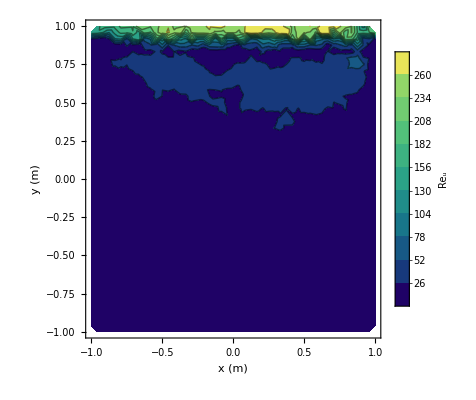

```mathematica
ListContourPlot[Transpose[{raw[[All, 8]], raw[[All, 9]], Abs[raw[[All, 12]]]*l/nu}], PlotRange->All, PlotLegends->BarLegend[All, LegendLabel->"Re_u"],ColorFunction->"BlueGreenYellow", Contours->10, FrameLabel->{"x (m)", "y (m)"}]
```

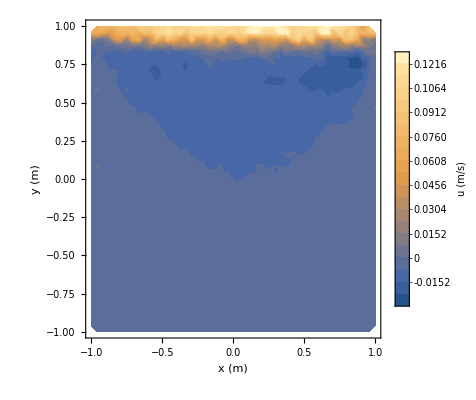

```mathematica
vxp=ListContourPlot[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 12]]}], PlotRange->All, PlotLegends->BarLegend[All, LegendLabel->"u (m/s)"], Contours->20, ContourStyle->None, FrameLabel->{"x (m)", "y (m)"}]
```

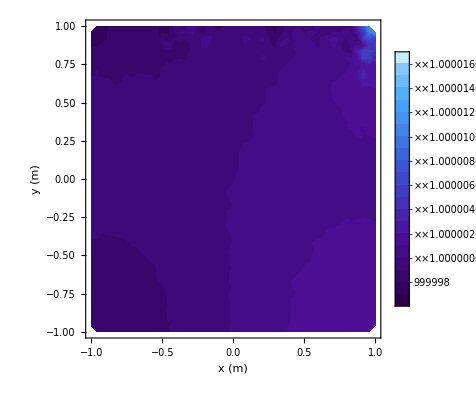

```mathematica
pxp=ListContourPlot[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 16]]}], PlotRange->All, PlotLegends->BarLegend[All, LegendLabel->"p (Pa)"], Contours->20, ContourStyle->None, FrameLabel->{"x (m)", "y (m)"},ColorFunction->"DeepSeaColors"]
```

```mathematica
Export["~/Dropbox/contour_vx.pdf", vxp]
```

~/Dropbox/contour_vx.pdf

```mathematica
c1=ImportString["\
itn 1 / 30, res 8.8759e+05
itn 2 / 30, res 8.9227e+05
itn 3 / 30, res 6.3024e+05
itn 4 / 30, res 4.9232e+05
itn 5 / 30, res 3.8639e+05
itn 6 / 30, res 3.0394e+05
itn 7 / 30, res 2.4064e+05
itn 8 / 30, res 1.9076e+05
itn 9 / 30, res 1.5182e+05
itn 10 / 30, res 1.2081e+05
itn 11 / 30, res 9.6760e+04
itn 12 / 30, res 8.0266e+04
itn 13 / 30, res 6.7768e+04
itn 14 / 30, res 5.7434e+04
itn 15 / 30, res 4.8677e+04
itn 16 / 30, res 4.1371e+04
itn 17 / 30, res 3.5113e+04
itn 18 / 30, res 3.0476e+04
itn 19 / 30, res 2.6629e+04
itn 20 / 30, res 3.1952e+04
itn 21 / 30, res 2.3587e+04
itn 22 / 30, res 3.9872e+04
itn 23 / 30, res 3.6867e+04
itn 24 / 30, res 5.1995e+04
itn 25 / 30, res 5.6088e+04
itn 26 / 30, res 7.0733e+04
itn 27 / 30, res 7.8378e+04
itn 28 / 30, res 9.2892e+04
itn 29 / 30, res 1.0102e+05
itn 30 / 30, res 1.1392e+05
", "Table", "FieldSeparators"->{" "}][[All, 6]];
```

```mathematica
c1fit=Fit[c1, {1, x, 1/x}, x]
```

148614.+948771./x-5957.34 x

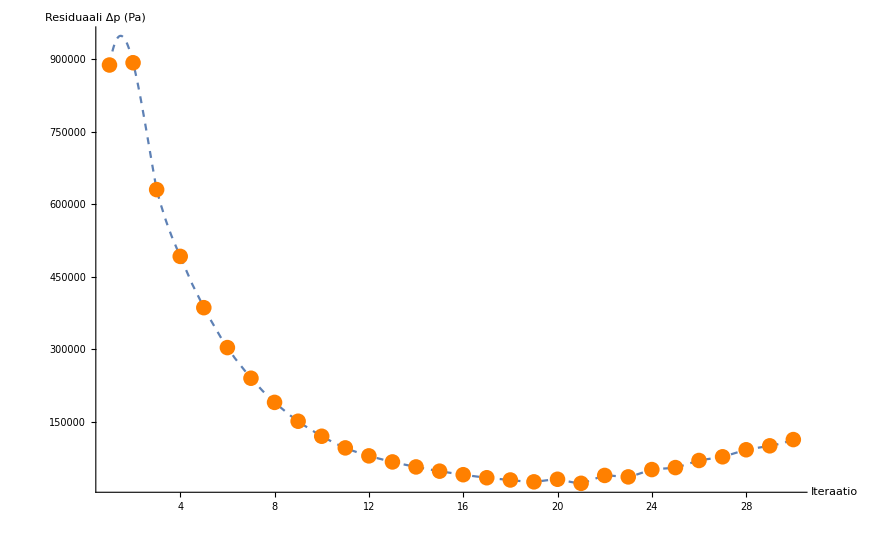

```mathematica
Show[(*Plot[c1fit, {x, 1, Length[c1]}, PlotStyle->LightGray, PlotRange->All],*)Plot[Interpolation[c1][x], {x, 1, Length[c1]}, PlotStyle->Dashed, PlotRange->All], ListPlot[c1, PlotStyle->Orange], AxesLabel->{"Iteraatio", "Residuaali Δp (Pa)"}, PlotRange->All, AxesOrigin->{1,0}]
```

```mathematica
Export["~/Dropbox/pxp.pdf", pxp];
```